## Loading data

import data as string:

```mathematica
data =Import[URLDownload["https://files.rcsb.org/download/2VF1.pdb1.gz"],"String"];
```

replace negative signs(-) with spaces to separate columns:

```mathematica
spaced  = StringReplace[data,"-"-> " -"];
```

export modified file to directory as text:

```mathematica
Export["/Users/Jihyeon/Desktop/2VF1_spaced.txt",spaced];
```

open modified file:

```mathematica
str = OpenRead["/Users/Jihyeon/Desktop/2VF1_spaced.txt"];
```

Read data starting from row 180:

```mathematica
Do[Read[str,"String"],278]
```

```mathematica
Read[str,"String"]
```

ATOM      1  N   ASP A  66      -48.858 216.608 174.133  1.00 47.16           N

read the list as words

```mathematica
fullrecord=ReadList[str,"Word", RecordLists->True];
```

split the list when consecutive first letter appears:

```mathematica
splitted = Split[fullrecord,First[#1]===First[#2]&];
```

remove unnecessary rows:

```mathematica
removed = DeleteCases[splitted,x_/;First[First[x]]== "TER"];
removed = DeleteCases[removed,x_/;First[First[x]]== "HETATM"];
removed = DeleteCases[removed,x_/;First[First[x]]== "MODEL"];
removed = DeleteCases[removed,x_/;First[First[x]]== "ENDMDL"];
removed = DeleteCases[removed,x_/;First[First[x]]== "MASTER"];
removed = DeleteCases[removed,x_/;First[First[x]]== "END"];
```

```mathematica
Dimensions[removed]
```

{120}

## Calculating center of mass

### extracting coordinates

only extract atom data and coordinates:

```mathematica
atom =   removed⟦All,All, -1⟧;
```

replace atoms with its atomic mass:

```mathematica
mass = atom/.{"N"->14.00, "C" -> 12.01, "O" -> 15.99, "S" -> 32.06};
```

extract x,y,z coordinates:

```mathematica
xcoor =  ToExpression[removed⟦All,All, 7⟧]
```

{1}
 |  |  |  |

```mathematica
ycoor =  ToExpression[removed⟦All,All, 8⟧]
```

{{217.24,216.181,215.161,217.932,218.941,219.405,219.282,216.426,215.487,215.421,214.404,215.859,217.197,218.388,217.486,219.4,4084,254.955,252.496,258.451,259.76,260.27,259.838,260.792,260.509,261.204,261.84,262.166,261.704,263.17,262.935,263.687,262.891},119}
 |  |  |  |

```mathematica
zcoor =  ToExpression[removed⟦All,All, 9⟧]
```

{{173.26,172.759,172.209,172.065,171.369,170.267,171.92,172.954,172.521,171.002,170.451,173.135,172.698,173.364,171.49,172.643,4084,229.059,228.441,227.713,228.132,229.52,230.088,227.065,226.521,230.034,231.355,231.714,232.786,231.464,231.02,232.921,230.935},119}
 |  |  |  |

```mathematica
chain = removed⟦All,All, 5⟧
```

{1}
 |  |  |  |

### Calculation

equation for calculating center of mass:

```mathematica
calcx[mass_,xcoor_] :=Sum[mass[[i]]* xcoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
xset = MapThread[calcx, {mass, xcoor}];
```

```mathematica
calcy[mass_,ycoor_] :=Sum[mass[[i]]* ycoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
yset = MapThread[calcy, {mass, ycoor}];
```

```mathematica
calcz[mass_,zcoor_] :=Sum[mass[[i]]* zcoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
zset = MapThread[calcz, {mass, zcoor}];
```

put all x, y, z center of mass coordinates together:

```mathematica
totcentercoor[xset_,yset_,zset_] :=List[xset, yset, zset]
centercoor = MapThread[totcentercoor, {xset, yset, zset}];
```

## Graphing points in 3D

```mathematica
flatchain = Flatten@chain;
```

```mathematica
x = Flatten[xcoor];
y = Flatten[ycoor];
z = Flatten[zcoor];
```

Put all x,y,z coordinates together:

```mathematica
totcoor[x_,y_,z_] :=List[x, y, z]
allcoor = MapThread[totcoor, {x, y, z}];
```

Match color with each protein:

```mathematica
colorlist = ToExpression[flatchain/.{"A"-> "Blue", "B" -> "Pink", "C" -> "Green", "D" -> "Red"}];
```

```mathematica
Graphics3D[{Point[allcoor,VertexColors->colorlist]}, Lighting->Automatic, Boxed->False]
```

-Graphics3D-

Match color with chain type for each center of mass coordinates:

```mathematica
chaintype = First /@ chain;
```

```mathematica
colorlist2 = ToExpression[chaintype/.{"A"-> "Blue", "B" -> "Pink", "C" -> "Green", "D" -> "Red"}];
```

Generate point cloud with center of mass:

```mathematica
Graphics3D[{PointSize[0.02],Point[centercoor,VertexColors->colorlist2]}]
```

-Graphics3D-

Create surface mesh to see general structure:

```mathematica
ListSurfacePlot3D[centercoor, BoxRatios->{1, 1, 1}]
```

-Graphics3D-

## Tiling

### Generate mesh

```mathematica
cm =RegionBoundary@DelaunayMesh@centercoor
```

-Graphics3D-

### Generate tiling

```mathematica
normal[Polygon[{p1_,p2_,p3_}]]:=Normalize@Cross[p1-p2,p1-p3]
```

```mathematica
delaunaymesh = DelaunayMesh@centercoor;
trianglecomponents = MeshPrimitives[RegionBoundary@delaunaymesh,2];
```

```mathematica
normals=normal/@trianglecomponents;
```

```mathematica
rounded = Round[normals,0.133888];
```

```mathematica
tally = Tally[rounded];
```

```mathematica
Tally[Last/@tally]
```

{{2,44},{1,112},{3,12}}

```mathematica
pent = GatherBy[tally,Last][[3]];
quad =  GatherBy[tally,Last][[1]];
tri =  GatherBy[tally,Last][[2]];
```

```mathematica
pentcoor = First /@ pent;
quadcoor = First /@ quad;
tricoor = First /@ tri;
```

```mathematica
value1 = Flatten /@ Map[Position[ rounded, #]&, pentcoor];
value2 = Flatten /@ Map[Position[ rounded, #]&, quadcoor];
value3 = Flatten /@ Map[Position[ rounded, #]&, tricoor];
```

```mathematica
coors1 = Map[Part[trianglecomponents,#] &, value1];
coors2 = Map[Part[trianglecomponents,#] &, value2];
coors3 = Map[Part[trianglecomponents,#] &, value3];
```

```mathematica
flat = Flatten[Map[ReplaceAll[Polygon->List][#] &, coors3],2];
subset = Map[Subsets[#, {2}]&,flat];
```

```mathematica
distance = Round[Apply[EuclideanDistance, subset, {2}],0.1];
equilateral[{x_,y_,z_}]:=(If[x==y==z,Return[1]])
```

```mathematica
positions = Flatten[ Position[equilateral /@ distance,1],1];
```

```mathematica
center = Map[Part[coors3,#] &, positions];
```

```mathematica
graphed = Graphics3D[{White, Point[Mean/@ pentcoorext],Blue,EdgeForm[],coors1,Pink,EdgeForm[],coors2, Yellow,EdgeForm[{Thick, Black}], coors3, Green, EdgeForm[], center}, Lighting->Automatic, Boxed->False]
```

-Graphics3D-

#### Projecting onto plane

```mathematica
extracted[{Polygon[{r1_,r2_,r3_}],Polygon[{t1_,t2_,t3_}],Polygon[{y1_,y2_,y3_}]}]:= List[{r1,r2,r3,t1,t2,t3,y1,y2,y3}]
pentcoorext = DeleteDuplicates/@Flatten[extracted /@ coors1,1];
path1 = Last /@ FindShortestTour /@ pentcoorext;
pentfinal =  Map[Take[#,5]&,MapThread[Part, {pentcoorext,path1}]];
```

```mathematica
extracted2[{Polygon[{r1_,r2_,r3_}],Polygon[{t1_,t2_,t3_}]}]:= List[{r1,r2,r3,t1,t2,t3}]
quadextract = DeleteDuplicates/@Flatten[extracted2 /@ coors2,1];
path2 = Last /@ FindShortestTour /@ quadextract;
quadfinal =  Map[Take[#,4]&,MapThread[Part, {quadextract,path2}]];
```

```mathematica
extracted3[{Polygon[{r1_,r2_,r3_}]}]:= List[{r1,r2,r3}]
triextract = DeleteDuplicates/@Flatten[extracted3 /@ coors3,1];
path3 = Last /@ FindShortestTour /@ triextract;
trifinal =  Map[Take[#,3]&,MapThread[Part, {triextract,path3}]];
```

```mathematica
pentcenter = Mean/@ pentcoorext
```

{{113.692,-15.2294,-21.889},{43.3023,56.1623,-92.777},{26.9946,-65.5365,-92.8069},{70.033,90.8344,21.9394},{43.6466,-106.078,21.891},{-43.3023,-56.1623,92.777},{-43.6466,106.078,-21.891},{70.2482,-9.43195,92.8094},{-26.9946,65.5365,92.8069},{-70.033,-90.8344,-21.9394},{-113.692,15.2294,21.889},{-70.2458,9.43579,-92.8081}}

```mathematica
centerfinal = Flatten[center/.Polygon->List,2];
```

```mathematica
projector[projectingPoint_]:=Module[{a,b,c,d,nv,k},
{a,b,c}=Flatten[center[[9]]/.Polygon->List,2];
nv=Cross[b-a,c-a];
d=-nv.a;
k=(-d-nv.projectingPoint)/Norm[nv]^2;
projectingPoint+k*nv
]&;
```

```mathematica
Map[projector, Part[centerfinal,{1,2,4}],{2}]
```

{{{117.569,393.944,181.403},{83.0219,412.354,198.619},{97.6908,383.107,230.243}},{{-65.6205,495.171,266.143},{-41.6101,458.554,297.458},{-28.7242,469.736,258.244}},{{32.0057,512.773,90.9947},{-11.8824,538.553,108.52},{9.77836,508.96,130.518}}}

```mathematica
object = 
Graphics3D[{
Polygon/@ Map[projector, Part[pentfinal,{2,4,5}],{2}],
center[[9]],
Polygon@{{44.93806550198935,422.99661649246696,235.13434714776267},{69.18544082323761,391.01880968327004,257.67241387931296},{97.69079612098935,383.1071894259724,230.24276430175652},{83.02186162078864,412.35438429592256,198.61876262610377}},
Polygon@{{-0.47885255671289784,423.33745627165126,301.1195654837659},{1.8831681185930416,442.9706410364924,261.9861535777255},{-28.724220109219186,469.7363493601107,258.2444386653498},{-41.61012564178391,458.5539261845303,297.45794880005127}},
Polygon/@ Map[projector, Part[centerfinal,{1,2,4}],{2}],
Polygon/@Map[projector,Part[quadfinal,{13,15,19,11,14,36,27}],{2}],
Polygon/@Map[projector,Part[trifinal,{14,37,15,38,41,42}],{2}]
}]
```

-Graphics3D-

```mathematica
Show[object,ViewPoint->{1.3,-2.4,2.}, Boxed->False, Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
{u,v,w}=center[[9,1,1]]
```

{{43.7255,442.665,201.179},{20.6776,479.126,168.736},{-0.327071,469.26,217.466}}

```mathematica
b=Orthogonalize[{v-u,w-u,Cross[v-u,w-u]}]
```

{{-0.427021,0.675538,-0.601084},{-0.69591,0.17893,0.695481},{0.577376,0.715285,0.393707}}

```mathematica
i=Inverse[b]
```

{{-0.427021,-0.69591,0.577376},{0.675538,0.17893,0.715285},{-0.601084,0.695481,0.393707}}

```mathematica
Planarize[x_,{u_,v_,w_}]:=x.Inverse[Orthogonalize[{v-u,w-u,Cross[v-u,w-u]}]]
```

orthogonalization:

```mathematica
pentproj = Map[projector, Part[pentfinal,{2,4,5}],{2}];
triproj = center[[9,1,1]];
ex1 ={{44.93806550198935,422.99661649246696,235.13434714776267},{69.18544082323761,391.01880968327004,257.67241387931296},{97.69079612098935,383.1071894259724,230.24276430175652},{83.02186162078864,412.35438429592256,198.61876262610377}};
ex2 ={{-0.47885255671289784,423.33745627165126,301.1195654837659},{1.8831681185930416,442.9706410364924,261.9861535777255},{-28.724220109219186,469.7363493601107,258.2444386653498},{-41.61012564178391,458.5539261845303,297.45794880005127}};
triexproj = Map[projector, Part[centerfinal,{1,2,4}],{2}];
quadproj = Map[projector,Part[quadfinal,{13,15,19,11,14,36,27}],{2}];
backproj = Map[projector,Part[trifinal,{14,37,15,38,41,42}],{2}];
```

```mathematica
pentextcoors = Map[Planarize[#,center[[9,1,1]]]&, pentproj ];
triextcoors = Map[Planarize[#,center[[9,1,1]]]&, triproj ];
quadextcoors =Map[Planarize[#,center[[9,1,1]]]&, quadproj ];
backextcoors = Map[Planarize[#,center[[9,1,1]]]&, backproj ];
triexcoors = Map[Planarize[#,center[[9,1,1]]]&, triexproj ];
ex1coors = Map[Planarize[#,center[[9,1,1]]]&, ex1 ];
ex2coors = Map[Planarize[#,center[[9,1,1]]]&, ex2 ];
```

```mathematica
map[x_]:= Map[Drop[#,-1]&,x]
```

```mathematica
pentflat=Polygon/@ map/@pentextcoors;
triflat=Polygon@Map[Drop[#,-1]&,triextcoors]
quadflat=Polygon/@map/@quadextcoors;
backflat = Polygon /@ map /@ backextcoors;
triexflat = Polygon /@ map /@ triexcoors;
ex1flat=Polygon@Map[Drop[#,-1]&,ex1coors]
ex2flat=Polygon@Map[Drop[#,-1]&,ex2coors]
```

Polygon[{{159.44,188.693},{213.414,188.693},{186.427,235.436}}]

Polygon[{{125.225,207.945},{79.7218,201.024},{78.6923,160.695},{123.723,154.142}}]

Polygon[{{105.187,285.504},{140.964,260.157},{174.364,283.644},{148.742,317.882}}]

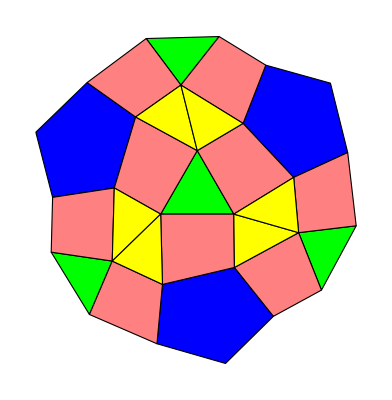

```mathematica
Graphics[{Tooltip[ {EdgeForm[{Thick,Black}],Blue,pentflat},ImageResize[Import[pentimg],{150}]],Tooltip[{EdgeForm[{Thick,Black}],Green,triflat},"ChainB"],
Tooltip[{EdgeForm[{Thick,Black}],Green,triexflat},"ChainB"],Tooltip[ {EdgeForm[{Thick,Black}],Pink,quadflat},"ChainB"],
Tooltip[ {EdgeForm[{Thick,Black}],Pink,ex1flat},"ChainB"],
Tooltip[ {EdgeForm[{Thick,Black}],Pink,ex2flat},"ChainB"],Tooltip[ {EdgeForm[{Thick,Black}],Yellow,backflat},"ChainA"]}]
```

```mathematica
pentimg = "/Users/Jihyeon/Desktop/pent.jpg";
ImageResize[Import[pentimg],{150}]
```

-Graphics-